length = Length[oscillatingDataSet]-1 = 830176

Separate time and angle from data set

Find Peaks

Peaks = {{412847/2,-0.302662},{436241,-0.293426},{1337595/2,-0.29505}}

Number of peaks = 3

Recombine peaks and associated time

Set::partw: Part 2 of {{0,0}} does not exist.

peaksAndTime = {{0,0},{16437.,-0.293426},{16934.9,-0.29505}}

Number of troughs = 1

troughsAndTime = {{0,0}}

Number of regression points = 4

regressionPoints = {{16437.,-0.293426},{16934.9,-0.29505},{16686.,-0.436521},{0,0}}

Compute wave properties

projectedEquilibrium =(peaksAndTime[[startingPeakIndex,2]]+ troughsAndTime[[1,2]])/2 = -0.146713

angleAmplitude = PeaksAndTime[[startingPeakIndex,2]] - projectedEquilibrium = -0.146713

period = peaksAndTime[[startingPeakIndex + 1,1]]- peaksAndTime[[startingPeakIndex,1]] = 497.937

distanceAmplitude = convertDegreesToRadians[angleAmplitude] * leverArmAxisToPendulumMassCenter = -0.000128031 meters

YComponentVelocity = (1/2)distanceAmplitude/(period/4) = -5.14247×10^-7 meters per second

energy = (1/2)(2/5)pendulumMass * YComponentVelocity^2 = 2.02568×10^-15

dampingCoefficient = peaksAndTime[[startingPeakIndex,2]]- peaksAndTime[[startingPeakIndex + 1,2]] = 0.00162414

startTime = peaksAndTime[[startingPeakIndex,1]] = 16437.

endTime = time[[length]] = 17280.6

pendulumMassMomentOfInertia = 2 pendulumMass(leverArmAxisToPendulumMassCenter + (2/5)pendulumMassRadius)^2 = 0.000217416

springConstantK = (4 Pi^2 pendulumMassMomentOfInertia) / testCase2Period^2 = 3.4618×10^-8

{3}

-Graphics-

FittedModel[-0.000127704-0.000020466 t]

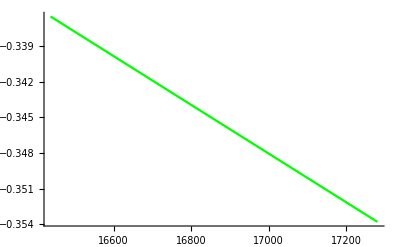

-Graphics-

```mathematica
analyzeZoeDataSet[dynamic2FRun1TimeSteadyStateDataSet]
dataSetPlot=ListLinePlot[{dynamic2FRun1TimeSteadyStateDataSet, peaksAndTime, troughsAndTime},PlotRange->{{startTime,endTime},{.1,-1.0}},PlotLabels->{"Run 2d6 Time Oscillating","Run 2d6 Peaks", "Run 2d6 Troughs"},PlotStyle->{Blue, Red, Red}]
model = LinearModelFit[linearRegressionTable, t, t]
regressionPlot =Plot[model["BestFit"], {t, startTime, endTime},PlotRange->{{startTime,endTime},{.1,-1.0}},PlotLabels->{"Regression"},PlotStyle->{Green}]
g1 =Show[dataSetPlot, regressionPlot]
(*analyzeZoeDataSet[dynamic2FRun1TimeOscillatingDataSet]
dataSetPlot=ListLinePlot[{dynamic2FRun1TimeOscillatingDataSet, peaksAndTime, troughsAndTime},PlotRange->{{startTime,endTime},{.1,-1.0}},PlotLabels->{"Run 2F1 Oscillating","Run 2f1 Peaks", "Run 2f1 Troughs"},PlotStyle->{Blue, Red, Red}]
model = LinearModelFit[linearRegressionTable, t, t]
regressionPlot =Plot[model["BestFit"], {t, startTime, endTime},PlotRange->{{startTime,endTime},{.1,-1.0}},PlotLabels->{"Regression"},PlotStyle->{Green}]
g2 =Show[dataSetPlot, regressionPlot]
Show[g1,g2]*)
```